```mathematica
(*Work in units a=1*)
(*Define regularized step function*)
st[ω_,x_]:=Exp[ω](UnitStep[x]+I Gamma[0,ω(I x+1)]/(2Pi))-Exp[-ω]I Gamma[0,ω(I x -1)]/(2Pi)
```

```mathematica
(*Self-energy: Σ(ω)=(J_⊥/2π)^2 σ(ω).*)
σ[ω_]:=Exp[ω]Gamma[0,ω+10^-10 I]-Exp[-ω]Gamma[0,-ω-10^-10 I]
```

```mathematica
(*We evaluate cor=|<d^*ψ(x)>|^2 at 20 exponentially spaced points between a/2 and 700a. We define (J_⊥)^2/4π = c. We evaluate the correlator at 3 values of c, namely 1/75, 1/250 and 1/1000*) 
xarray=Table[0.5Exp[(Log[700]-Log[0.5])n/19],{n,0,19}];
carray={1/75};
barray={0,0.2,0.4,0.6,0.8,1};
```

```mathematica
magcor[b_,x_]:= Abs[NIntegrate[Exp[I ω x](st[ω,x]/(ω- σ[ω]/(75 Pi)+I b)-st[ω,-x]/(ω- Conjugate[σ[ω]]/(75Pi)-I b))/(2Pi),{ω,-20,0},Method->"GlobalAdaptive",MaxRecursion->20]]^2
```

```mathematica
magcorarray=Table[{xarray[[n]],magcor[barray[[m]],xarray[[n]]]},{m,1,6},{n,1,20}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

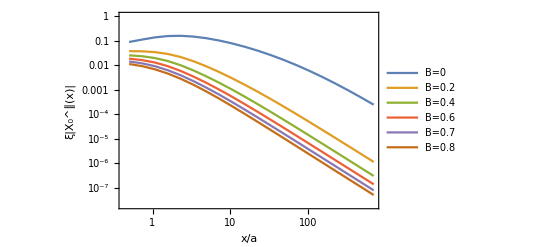

```mathematica
p3=ListLogLogPlot[magcorarray,Joined->True,BaseStyle->{FontSize->14,FontFamily->"Helvetica"},Frame->True,Axes->False,FrameLabel->{"x/a","ξ|X_0^∥(x)|"},PlotLegends->{"B=0","B=0.2","B=0.4","B=0.6","B=0.7","B=0.8","B=1"}];
Show[p3]
```